# Ising Model: Bryan Foley

## Temperature Sweep, Constant Magnetic Field

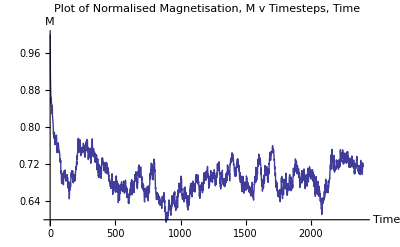

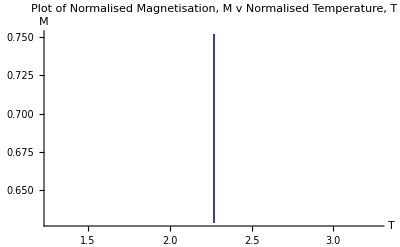

```mathematica
ClearAll[t,k,i,j,n,H]
L=20;                  (* length *)
L2=L L;                (* total number *)
H= 0.;                (* = H/k *)
f[x_]:= x (-1);        (* spin flip operator *)
J= 1.0;             (* = J/k *) 
m={};
e={};
gra = {};
currentMag=0;
currentEnergy=0;
avgMag={};
avgEnergy={};
n=0;
k=1;
mTemp=0;
eTemp=0;
Mag={};
Energy={};
dw = 0;
temp = {};
spin[i_,j_,ls_,L_]:=Module[{j1,j2,k1,k2,temp},
j1=i+1;
j2=j+1; 
k1=i-1;
k2=j-1;

If[j1>L,j1=1;];
If[j2>L,j2=1;];
If[k1<1,k1=L;];
If[k2<1,k2=L;];

temp = ls[[j1,j]]+ls[[k1,j]]+ls[[i,j2]]+ls[[i,k2]];
Return[temp]
];

(* random spin system *)
SeedRandom[];
(*----------------------------------Initialise--------------------------------*)
points=25;
Tinit=2.27;
Tfinal=5;
passes=100;

(*dt=(Tfinal - Tinit)/(points - 1);*)
dt = 0;
t=Tinit;
(*-----------------------------------InitSpin---------------------------------*)
(*Create a table of 1's and 0's*)
ml=Table[Random[Integer],{L},{L}];

(*Replace the 0's with 1's*)
For[j=1,j<=Length[ml],j++,
   For[i=1,i<=Length[ml],i++,
      If[ml[[j,i]]==0,ml[[j,i]]=1];
If[ml[[j,i]]==1,ml[[j,i]]=1];
];
];
gra= Append[gra,ArrayPlot[ml,ColorRules->{1->Red,-1->Blue}]];
(*Initialise the mag and energy of the system*)
(*All spin up state*)
(*m=Append[m,L2];*)
(*e=Append[e,-2*L2];*)

(* Metropolis methods with cyclic boudary condition *)
For[i=1,i<points,i++,

(*Reset the lattice to all Spin up state*)
For[b=1,b<=Length[ml],b++,
   For[a=1,a<=Length[ml],a++,
      If[ml[[b,a]]==0,ml[[b,a]]=1];
If[ml[[b,a]]==1,ml[[b,a]]=1];
];
];

For[c=1,c<=L,c++,
For[d=1,d<=L,d++,
currentMag = currentMag+ml[[c,d]]; 
];
];
m = Append[m,currentMag];
(*-------------------------------------Calculate--------------------------------*)
mTemp=0;
eTemp=0;
n=0;
(*currentMag = 0;*)
(*m=Append[m,currentMag];
e=Append[e,currentEnergy];*)
For[j=1,j<passes,j++,
For[i1=1,i1<=L,i1++,
For[i2=1,i2<=L,i2++,
      (*---------------------------------Neighbours---------------------------------*)
j1=i1+1;
j2=i2+1; 
k1=i1-1;
k2=i2-1;
        (*---------------------------------Test for Edge---------------------------------*)
If[j1>L,j1=1;];
If[j2>L,j2=1;];
If[k1<1,k1=L;];
If[k2<1,k2=L;];
   (*---------------------------------Test for flip---------------------------------*)
dG=ml[[j1,i2]]+ml[[k1,i2]]+ml[[i1,j2]]+ml[[i1,k2]];(*Sum of the Spins*)
dE=-2f[ml[[i1,i2]]]*(J*dG+H);(*Energy to Flip*)

If[(dE<0),(*If it would decrease the energy, flip*)
ml=MapAt[f,ml,{{i1,i2}}];
currentMag=currentMag+2*(ml[[i1,i2]]);
currentEnergy=currentEnergy+dE
];
dW=N[Exp[-dE/t]];(*Boltzmann Energy*)
If[(dW<1 && dW>Random[]),
ml=MapAt[f,ml,{{i1,i2}}];
currentMag=currentMag+2*(ml[[i1,i2]]);
currentEnergy=currentEnergy+dE
]
(*---------------------------------End inner loop---------------------------------*)
](*Inner Loop, i2*)
(*---------------------------------End inner loop---------------------------------*)
];(*Inner Loop, i1*)
gra= Append[gra,ArrayPlot[ml,ColorRules->{1->Red,-1->Blue}]];
m=Append[m,currentMag];
e=Append[e,currentEnergy];
If[j> passes/2,
mTemp=mTemp+currentMag;
eTemp=eTemp+currentEnergy;
n=n+1]
(*---------------------------------End Inner Loop---------------------------------*)
];(*Inner Loop, n_passes*)
avgMag=mTemp/n;
avgEnergy=eTemp/n;
Mag=Append[Mag,avgMag];
Energy=Append[Energy,avgEnergy];
temp = Append[temp,t];
t = t+ dt;
mTemp = 0;
eTemp = 0;
currentMag = 0;
currentEnergy = 0
(*---------------------------------End Outer Loop---------------------------------*)
];(*Outer Loop, n_points*)
ListLinePlot[m/L2,PlotRange->All,PlotLabel->"Plot of Normalised Magnetisation, M v Timesteps, Time",AxesLabel->{Time,M},LabelStyle->Directive[Bold]]
ListLinePlot[Table[{temp[[i]],Mag[[i]]/L2},{i,1,Length[temp]}],PlotRange->All,PlotLabel->"Plot of Normalised Magnetisation, M v Normalised Temperature, T",AxesLabel->{T,M},LabelStyle->Directive[Bold]]
ListAnimate[gra];
```

```mathematica
ListLinePlot[m/L2,PlotRange->All,PlotLabel->"Plot of Normalised Magnetisation, M v Timesteps, t",AxesLabel->{Time,M},LabelStyle->Directive[Bold]]
ListLinePlot[Table[{temp[[i]],Mag[[i]]/L2},{i,1,Length[temp]}],PlotRange->All,PlotLabel->"Plot of Normalised Magnetisation, M v Normalised Temperature, T",AxesLabel->{T,M},LabelStyle->Directive[Bold]]
```

## Mag. Field Sweep, Constant Temperature

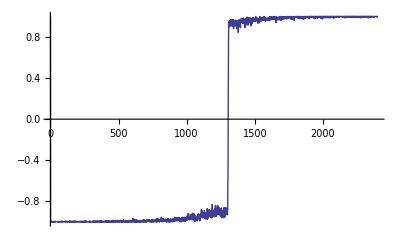

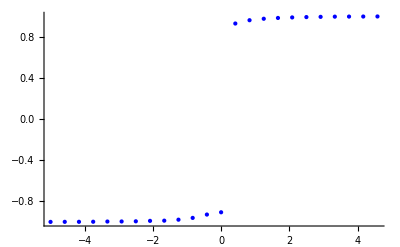

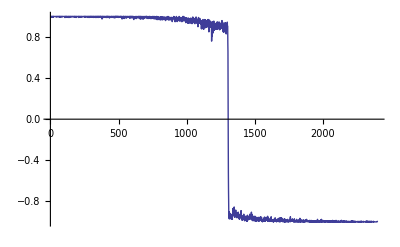

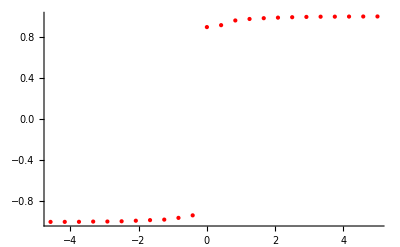

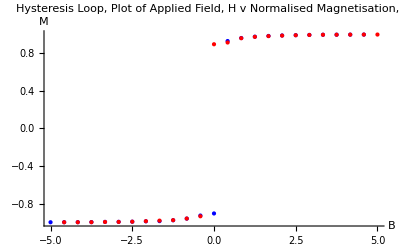

```mathematica
t=2.27;
passes = 100;
points=25;
(*---------------------------------FORWARDS---------------------------------*)
ClearAll[k,i,j,n,H]
L=20;                  (* length *)
L2=L L;                (* total number *)
H= -3.;                (* = H/k *)
f[x_]:= x (-1);        (* spin flip operator *)
J= 1.0;             (* = J/k *) 
m={};
e={};
gra = {};
currentMag=0;
currentEnergy=0;
avgMag={};
avgEnergy={};
n=0;
k=1;
mTemp=0;
eTemp=0;
Mag={};
Energy={};
dw = 0;
field = {};
spin[i_,j_,ls_,L_]:=Module[{j1,j2,k1,k2,temp},
j1=i+1;
j2=j+1; 
k1=i-1;
k2=j-1;

If[j1>L,j1=1;];
If[j2>L,j2=1;];
If[k1<1,k1=L;];
If[k2<1,k2=L;];

temp = ls[[j1,j]]+ls[[k1,j]]+ls[[i,j2]]+ls[[i,k2]];
Return[temp]
];

(* random spin system *)
SeedRandom[];
(*----------------------------------Initialise--------------------------------*)
Hinit=-5.;
Hfinal=5;

dh=(Hfinal - Hinit)/(points - 1);
(*dt = 0;*)
H=Hinit;
(*-----------------------------------InitSpin---------------------------------*)
(*Create a table of 1's and 0's*)
ml=Table[Random[Integer],{L},{L}];

(*Replace the 0's with 1's*)
For[j=1,j<=Length[ml],j++,
   For[i=1,i<=Length[ml],i++,
      If[ml[[j,i]]==0,ml[[j,i]]=1];
If[ml[[j,i]]==1,ml[[j,i]]=1];
];
];
gra= Append[gra,ArrayPlot[ml,ColorRules->{1->Red,-1->Blue}]];
(*Initialise the mag and energy of the system*)
(*All spin up state*)
(*m=Append[m,L2];*)
(*e=Append[e,-2*L2];*)

(* Metropolis methods with cyclic boudary condition *)
For[i=1,i<points,i++,

(*Reset the lattice to all Spin up state*)
For[b=1,b<=Length[ml],b++,
   For[a=1,a<=Length[ml],a++,
      If[ml[[b,a]]==0,ml[[b,a]]=1];
If[ml[[b,a]]==1,ml[[b,a]]=1];
];
];

For[c=1,c<=L,c++,
For[d=1,d<=L,d++,
currentMag = currentMag+ml[[c,d]]; 
];
];
m = Append[m,currentMag];
(*-------------------------------------Calculate--------------------------------*)
mTemp=0;
eTemp=0;
n=0;
(*currentMag = 0;*)
(*m=Append[m,currentMag];
e=Append[e,currentEnergy];*)
For[j=1,j<passes,j++,
For[i1=1,i1<=L,i1++,
For[i2=1,i2<=L,i2++,
      (*---------------------------------Neighbours---------------------------------*)
j1=i1+1;
j2=i2+1; 
k1=i1-1;
k2=i2-1;
        (*---------------------------------Test for Edge---------------------------------*)
If[j1>L,j1=1;];
If[j2>L,j2=1;];
If[k1<1,k1=L;];
If[k2<1,k2=L;];
   (*---------------------------------Test for flip---------------------------------*)
dG=ml[[j1,i2]]+ml[[k1,i2]]+ml[[i1,j2]]+ml[[i1,k2]];(*Sum of the Spins*)
dE=-2f[ml[[i1,i2]]]*(J*dG+H);(*Energy to Flip*)

If[(dE<0),(*If it would decrease the energy, flip*)
ml=MapAt[f,ml,{{i1,i2}}];
currentMag=currentMag+2*(ml[[i1,i2]]);
currentEnergy=currentEnergy+dE
];
dW=N[Exp[-dE/t]];(*Boltzmann Energy*)
If[(dW<1 && dW>Random[]),
ml=MapAt[f,ml,{{i1,i2}}];
currentMag=currentMag+2*(ml[[i1,i2]]);
currentEnergy=currentEnergy+dE
]
(*---------------------------------End inner loop---------------------------------*)
](*Inner Loop, i2*)
(*---------------------------------End inner loop---------------------------------*)
];(*Inner Loop, i1*)
gra= Append[gra,ArrayPlot[ml,ColorRules->{1->Red,-1->Blue}]];
m=Append[m,currentMag];
e=Append[e,currentEnergy];
If[j> passes/2,
mTemp=mTemp+currentMag;
eTemp=eTemp+currentEnergy;
n=n+1]
(*---------------------------------End Inner Loop---------------------------------*)
];(*Inner Loop, n_passes*)
avgMag=mTemp/n;
avgEnergy=eTemp/n;
Mag=Append[Mag,avgMag];
Energy=Append[Energy,avgEnergy];
field = Append[field,H];
H = H+dh;
mTemp = 0;
eTemp = 0;
currentMag = 0;
currentEnergy = 0
(*---------------------------------End Outer Loop---------------------------------*)
];(*Outer Loop, n_points*)
ListLinePlot[m/L2,PlotRange->All]
PlotF =ListPlot[Table[{field[[i]],Mag[[i]]/L2},{i,1,Length[field]}],PlotRange->All,PlotStyle->{Thick, Blue}]
ListAnimate[gra];
(*---------------------------------BACKWARDS---------------------------------*)
ClearAll[k,i,j,n,H]
L=20;                  (* length *)
L2=L L;                (* total number *)
f[x_]:= x (-1);        (* spin flip operator *)
J= 1.0;             (* = J/k *) 
m={};
e={};
gra = {};
currentMag=0;
currentEnergy=0;
avgMag={};
avgEnergy={};
n=0;
k=1;
mTemp=0;
eTemp=0;
Mag={};
Energy={};
dw = 0;
field = {};
spin[i_,j_,ls_,L_]:=Module[{j1,j2,k1,k2,temp},
j1=i+1;
j2=j+1; 
k1=i-1;
k2=j-1;

If[j1>L,j1=1;];
If[j2>L,j2=1;];
If[k1<1,k1=L;];
If[k2<1,k2=L;];

temp = ls[[j1,j]]+ls[[k1,j]]+ls[[i,j2]]+ls[[i,k2]];
Return[temp]
];

(* random spin system *)
SeedRandom[];
(*----------------------------------Initialise--------------------------------*)
Hinit=-5.;
Hfinal=5;

dh=(Hfinal - Hinit)/(points - 1);
(*dt = 0;*)
H=Hfinal;
(*-----------------------------------InitSpin---------------------------------*)
(*Create a table of 1's and 0's*)
ml=Table[Random[Integer],{L},{L}];

(*Replace the 0's with 1's*)
For[j=1,j<=Length[ml],j++,
   For[i=1,i<=Length[ml],i++,
      If[ml[[j,i]]==0,ml[[j,i]]=1];
If[ml[[j,i]]==1,ml[[j,i]]=1];
];
];
gra= Append[gra,ArrayPlot[ml,ColorRules->{1->Red,-1->Blue}]];
(*Initialise the mag and energy of the system*)
(*All spin up state*)
(*m=Append[m,L2];*)
(*e=Append[e,-2*L2];*)

(* Metropolis methods with cyclic boudary condition *)
For[i=1,i<points,i++,

(*Reset the lattice to all Spin up state*)
For[b=1,b<=Length[ml],b++,
   For[a=1,a<=Length[ml],a++,
      If[ml[[b,a]]==0,ml[[b,a]]=1];
If[ml[[b,a]]==1,ml[[b,a]]=1];
];
];

For[c=1,c<=L,c++,
For[d=1,d<=L,d++,
currentMag = currentMag+ml[[c,d]]; 
];
];
m = Append[m,currentMag];
(*-------------------------------------Calculate--------------------------------*)
mTemp=0;
eTemp=0;
n=0;
(*currentMag = 0;*)
(*m=Append[m,currentMag];
e=Append[e,currentEnergy];*)
For[j=1,j<passes,j++,
For[i1=1,i1<=L,i1++,
For[i2=1,i2<=L,i2++,
      (*---------------------------------Neighbours---------------------------------*)
j1=i1+1;
j2=i2+1; 
k1=i1-1;
k2=i2-1;
        (*---------------------------------Test for Edge---------------------------------*)
If[j1>L,j1=1;];
If[j2>L,j2=1;];
If[k1<1,k1=L;];
If[k2<1,k2=L;];
   (*---------------------------------Test for flip---------------------------------*)
dG=ml[[j1,i2]]+ml[[k1,i2]]+ml[[i1,j2]]+ml[[i1,k2]];(*Sum of the Spins*)
dE=-2f[ml[[i1,i2]]]*(J*dG+H);(*Energy to Flip*)

If[(dE<0),(*If it would decrease the energy, flip*)
ml=MapAt[f,ml,{{i1,i2}}];
currentMag=currentMag+2*(ml[[i1,i2]]);
currentEnergy=currentEnergy+dE
];
dW=N[Exp[-dE/t]];(*Boltzmann Energy*)
If[(dW<1 && dW>Random[]),
ml=MapAt[f,ml,{{i1,i2}}];
currentMag=currentMag+2*(ml[[i1,i2]]);
currentEnergy=currentEnergy+dE
]
(*---------------------------------End inner loop---------------------------------*)
](*Inner Loop, i2*)
(*---------------------------------End inner loop---------------------------------*)
];(*Inner Loop, i1*)
gra= Append[gra,ArrayPlot[ml,ColorRules->{1->Red,-1->Blue}]];
m=Append[m,currentMag];
e=Append[e,currentEnergy];
If[j> passes/2,
mTemp=mTemp+currentMag;
eTemp=eTemp+currentEnergy;
n=n+1]
(*---------------------------------End Inner Loop---------------------------------*)
];(*Inner Loop, n_passes*)
avgMag=mTemp/n;
avgEnergy=eTemp/n;
Mag=Append[Mag,avgMag];
Energy=Append[Energy,avgEnergy];
field = Append[field,H];
H = H-dh;
mTemp = 0;
eTemp = 0;
currentMag = 0;
currentEnergy = 0
(*---------------------------------End Outer Loop---------------------------------*)
];(*Outer Loop, n_points*)
ListLinePlot[m/L2,PlotRange->All]
PlotB= ListPlot[Table[{field[[i]],Mag[[i]]/L2},{i,1,Length[field]}],PlotRange->All,PlotStyle->{Thick, Red}]
ListAnimate[gra];
Show[PlotF,PlotB,PlotLabel->"Hysteresis Loop, Plot of Applied Field, H v Normalised Magnetisation, M",AxesLabel->{B,M},LabelStyle->Directive[Bold]]
```